Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

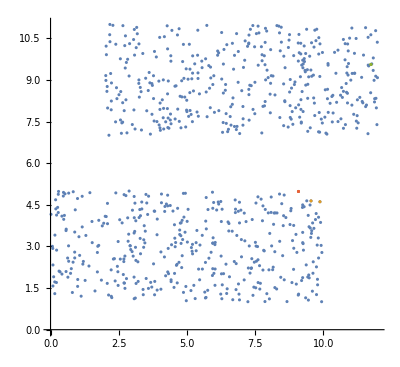

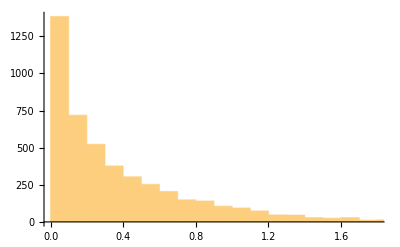

Nejbližší vysílač je na konvexní obálce v 5439 z 10000 případů.

Druhý vysílač hledaný stejnou metodou jako první byl stejný s druhým vysílačem hledaným na CH v 4571

Druhý vysílač hledaný stejnou metodou jako první byl stejný s druhým vysálačem hledaným ze všech v  569

Druhý vysílač hledaný stejnou metodou jako první byl stejný s prvním vysílačem hledaným ze všech v 0

Průměrná vzdálenost Transmitter -> Sink: 4.12975

Průměrná vzdálenost TransmitterOnCH -> Sink: 4.3008

Průměrná vzdálenost Transmitter2 -> Sink: 4.28024 První i druhý hledán mimo CH

Průměrná vzdálenost Transmitter2OnCH -> Sink: 4.91947 První i druhý hledán na CH

Průměrná vzdálenost Transmitter2OnCH -> Sink: 4.44537 První hledán na CH, druhý mimo

Průměrná vzdálenost Transmitter2OnCH2 -> Sink: 4.746 Druhý hledan stejně jako první na CH

Průměrná vzdálenost vysílačů pouze na konv. ob.: 1.32548

Průměrná vzdálenost vysílačů pouze na konv. ob. (druhý hledan stejně jako první): 1.8924

Průměrná vzdálenost vysílačů jeden mimo konv. ob.: 0.22967

Průměrná vzdálenost vysílačů při hledání ze všech: 0.228636

Při hledání druhého vysílače mimo konvexní obálku jsme dosáhli menší vzdálenosti v 9101 z 10000 případů.

Konvexní obálka přepočítána:

Průměrná vzdálenost Transmitter2OnCH2 -> Sink: 4.40064 Druhý hledan stejně jako první na CH

Průměrná vzdálenost vysílačů pouze na konv. ob. (druhý hledan stejně jako první): 1.29561

```mathematica
(*Global Variables*)
numOfPoints = 400;
numOfTests = 10000;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*(*Initialize of two CIRCLE regions*)
region1 = DiscretizeRegion@Disk[{10,10}, 10];
region2 = DiscretizeRegion@Disk[{30,30}, 10];*)

(*(*Initialize of two POLYGON regions*)
region1 = DiscretizeRegion@Polygon[{{2,1},{3,1},{4,2},{4,3},{3.75, 3.75}, {3, 4}, {2, 4}, {1, 3}, {1, 2}}];
region2 = DiscretizeRegion@Polygon[{{5,2}, {7,2}, {7,7}, {2,7}, {2, 5}, {4, 5}, {5, 4}}];*)

true = 0;
to = 0;
j = 0;
k = 0;
closer = 0;
closest = 0.0;
distTransmittersBothOnCH = 0.0;
distTransmittersBothOnCH2 = 0.0;
distTransmittersBothOnCH2r = 0.0;
distTransmittersOneOnCH = 0.0;
distTransmitters = 0.0;

distTransmitterSink = 0.0;
distTransmitterOnCHSink = 0.0;
distTransmitter2Sink = 0.0;
distTransmitter2OnCHSinka = 0.0;
distTransmitter2OnCHSinkb = 0.0;
distTransmitter2OnCH2Sink = 0.0;
distTransmitter2OnCH2Sinkr = 0.0;

distList={};
sink;

Do[
Module[{},

(*Initialize of two RECTANGLE regions*)
region1 = DiscretizeRegion@Rectangle[{0,1},{10,5}];
region2 = DiscretizeRegion@Rectangle[{2,7},{12,11}];

region1Centr = RegionCentroid[region1];
region2Centr = RegionCentroid[region2];

pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];
sink = RandomSample[pts2, 1];
area = Join[pts1, pts2];

lineCS = Line[{region1Centr, Flatten[sink, 1]}];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],(*Print[arrayOneConvexHull[[x]]]*), arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];


(*Find first transmitter on convex hull*)
transmitterOnCH = Flatten[Nearest[arrayOneConvexHull, sink],1];
(*Find second transmitter on convex hull*)
transmittersBothOnCH = Flatten[Nearest[arrayOneConvexHull,transmitterOnCH,{2,5}],1];
(*Find second transmitter from all points*)
transmittersOneOnCH =  Flatten[Nearest[pts1,transmitterOnCH,{2,5}],1];

(*Find second transmitter - delete the first from CH and start looking again nearest to sink on CH*)
p = Position[arrayOneConvexHull, transmitterOnCH[[1]]];
arrayOneConvexHull2 = Delete[arrayOneConvexHull, p];
transmitterOnCH2 = Flatten[Nearest[arrayOneConvexHull2, sink],1];


(*Find first transmitter from all points*)
transmitter = Flatten[Nearest[pts1, sink],1];
(*Find second transmitter from all points*)
transmitters = Flatten[Nearest[pts1,transmitter,{2,5}],1];

(*Distance first transmitter -> sink*)
r = EuclideanDistance[transmitterOnCH,sink];
distTransmitterOnCHSink += r;
s = EuclideanDistance[transmitter,sink];
distTransmitterSink += s;
(*Distance second transmitter -> sink*)
u = EuclideanDistance[transmitters[[2]],Flatten[sink,1]]; (*První i druhý hledán mimo CH*)
distTransmitter2Sink += u;
v = EuclideanDistance[transmittersBothOnCH[[2]],Flatten[sink,1]]; (*První i druhý hledán na CH*)
distTransmitter2OnCHSinka += v;
q = EuclideanDistance[transmittersOneOnCH[[2]],Flatten[sink,1]]; (*První hledán na CH, druhý mimo*)
distTransmitter2OnCHSinkb += q;
t = EuclideanDistance[transmitterOnCH2,sink];
distTransmitter2OnCH2Sink += t;


(*Distance transmitter -> transmitter*)
a= EuclideanDistance[transmittersBothOnCH[[1]],transmittersBothOnCH[[2]]];
b= EuclideanDistance[transmittersOneOnCH[[1]],transmittersOneOnCH[[2]]];
distTransmittersBothOnCH +=a;
distTransmittersOneOnCH += b;
If[(a > b),closer++];
c = EuclideanDistance[transmitters[[1]],transmitters[[2]]];
distTransmitters += c;
d =  EuclideanDistance[transmitterOnCH[[1]],Flatten[transmitterOnCH2,1]];
distTransmittersBothOnCH2 += d; 

(*If transmitterOnCH is really the nearest point to sink*)
If[(transmitter == transmitterOnCH), 
true++;
If[transmittersBothOnCH[[2]] == Flatten[transmitterOnCH2,1], to++];
If[transmitters[[2]] == Flatten[transmitterOnCH2,1], j++];
If[Flatten[transmitter,1] == Flatten[transmitterOnCH2,1], k++];
,(*If transmitter from all points is nearer to sink than transmitterOnCH*)
closest++;
(*Distance diff, how much is transmitterOnCH farrer to sink*)
t = r - s;
distList = Append[distList, t];
];

(*Znovu přepočítám Konvexní obálku bez nejbližšího vysílače*)
pr = Position[pts1, transmitterOnCH[[1]]];
pts1r = Delete[pts1, pr];
convexHullpts1r = RegionBoundary[ConvexHullMesh[pts1r]];
arrayOneConvexHullr = pts1r;
cutConvexHull1r[x_]=If[RegionMember[convexHullpts1r,arrayOneConvexHullr[[x]]],(*Print[arrayOneConvexHull[[x]]]*), arrayOneConvexHullr = Delete[arrayOneConvexHullr, x]];
For[i=numOfPoints-1, i>0, i--, cutConvexHull1r[i]];

transmitterOnCH2r = Flatten[Nearest[arrayOneConvexHullr, sink],1];
tr = EuclideanDistance[transmitterOnCH2r,sink];
distTransmitter2OnCH2Sinkr += tr;
e =  EuclideanDistance[transmitterOnCH[[1]],Flatten[transmitterOnCH2r,1]];
distTransmittersBothOnCH2r += e;

],{numOfTests}]

ListPlot[{area, transmittersOneOnCH, sink, transmitterOnCH2}, AspectRatio->Automatic]
Histogram[distList]

distTransmittersBothOnCH = distTransmittersBothOnCH/numOfTests;
distTransmittersOneOnCH = distTransmittersOneOnCH/numOfTests;
distTransmitters = distTransmitters/numOfTests;
distTransmittersBothOnCH2 = distTransmittersBothOnCH2 / numOfTests;
distTransmittersBothOnCH2r = distTransmittersBothOnCH2r / numOfTests;

distTransmitterSink = distTransmitterSink/numOfTests;
distTransmitterOnCHSink = distTransmitterOnCHSink/numOfTests;
distTransmitter2OnCHSinka  = distTransmitter2OnCHSinka / numOfTests;
distTransmitter2OnCHSinkb  = distTransmitter2OnCHSinkb / numOfTests;
distTransmitter2OnCH2Sink = distTransmitter2OnCH2Sink /numOfTests;
distTransmitter2Sink = distTransmitter2Sink / numOfTests;
distTransmitter2OnCH2Sinkr = distTransmitter2OnCH2Sinkr / numOfTests;

Print["Nejbližší vysílač je na konvexní obálce v ", true , " z ", numOfTests ," případů. "]
Print["Druhý vysílač hledaný stejnou metodou jako první byl stejný s druhým vysílačem hledaným na CH v ", to]
Print["Druhý vysílač hledaný stejnou metodou jako první byl stejný s druhým vysálačem hledaným ze všech v  ", j]
Print["Druhý vysílač hledaný stejnou metodou jako první byl stejný s prvním vysílačem hledaným ze všech v ", k]
Print[""]
Print["Průměrná vzdálenost Transmitter -> Sink: ", distTransmitterSink]
Print["Průměrná vzdálenost TransmitterOnCH -> Sink: ", distTransmitterOnCHSink ]
Print["Průměrná vzdálenost Transmitter2 -> Sink: ", distTransmitter2Sink, " První i druhý hledán mimo CH" ]
Print["Průměrná vzdálenost Transmitter2OnCH -> Sink: ", distTransmitter2OnCHSinka, " První i druhý hledán na CH"] 
Print["Průměrná vzdálenost Transmitter2OnCH -> Sink: ", distTransmitter2OnCHSinkb, " První hledán na CH, druhý mimo"] 
Print["Průměrná vzdálenost Transmitter2OnCH2 -> Sink: ", distTransmitter2OnCH2Sink, " Druhý hledan stejně jako první na CH" ]
Print[""]
Print["Průměrná vzdálenost vysílačů pouze na konv. ob.: ",distTransmittersBothOnCH]
Print["Průměrná vzdálenost vysílačů pouze na konv. ob. (druhý hledan stejně jako první): ",distTransmittersBothOnCH2]
Print["Průměrná vzdálenost vysílačů jeden mimo konv. ob.: ",distTransmittersOneOnCH]
Print["Průměrná vzdálenost vysílačů při hledání ze všech: ",distTransmitters]

Print["Při hledání druhého vysílače mimo konvexní obálku jsme dosáhli menší vzdálenosti v ", closer , " z ",numOfTests ," případů. "]
(*Print["Při hledání ze všech bodů byly nalezné body nejblíže sobě v  ", closest , " z ",numOfTests ," případů. "]*)
Print[""]
Print["Konvexní obálka přepočítána: "]
Print["Průměrná vzdálenost Transmitter2OnCH2 -> Sink: ", distTransmitter2OnCH2Sinkr, " Druhý hledan stejně jako první na CH" ]
Print["Průměrná vzdálenost vysílačů pouze na konv. ob. (druhý hledan stejně jako první): ",distTransmittersBothOnCH2r]
```